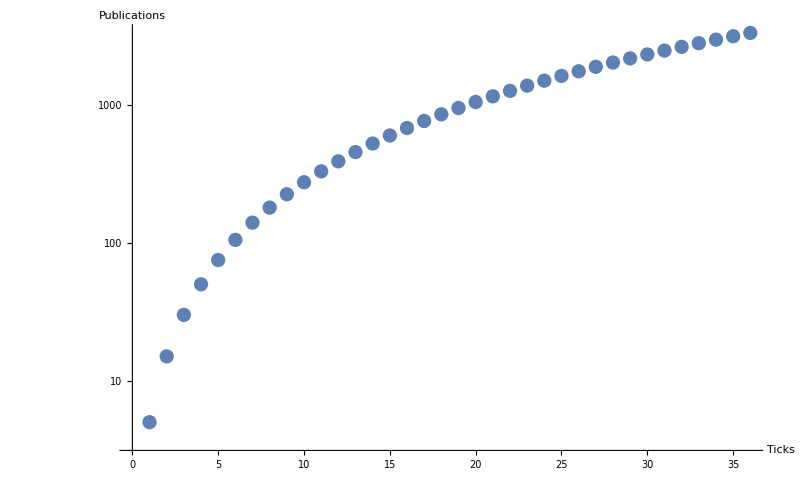

```mathematica
dataPublicationsCurve = Import["/home/fabianact/Tesis/Pruebas/ModelGrid/testTables/uno.csv"];
plotPublicationsCurve=ListLogPlot[{dataPublicationsCurve},ImageSize->800,AxesLabel->{"Ticks","Publications"}]
Export["publicationsCurve.png",plotPublicationsCurve];
```